```mathematica
Needs["DorisAlgorithmCompactCase`"]
```

```mathematica
g=-(x+1)x(x-1)(x-2)(x-3)(x-4);
DorisAlgorithmCompactCase[x,(x-2)(x-3),{g}]
```

True

```mathematica
Series[1+a^2((x-b)^2+c^2)(x+1)x(x-1)(x-4),{x,2,10}]
Series[1+a^2((x-b)^2+c^2)(x+1)x(x-1)(x-4),{x,3,10}]
```

(1-12 a^2 ((2-b)^2+c^2))-8 (a^2 (14-11 b+2 b^2+2 c^2)) (x-2)-a^2 (80-36 b+b^2+c^2) (x-2)^2+a^2 (-20+2 b+4 ((2-b)^2+c^2)) (x-2)^3+a^2 (-1+4 (4-2 b)+(2-b)^2+c^2) (x-2)^4+a^2 (8-2 b) (x-2)^5+a^2 (x-2)^6+O[x-2]^11

(1-24 a^2 ((3-b)^2+c^2))-2 (a^2 (81-30 b+b^2+c^2)) (x-3)+a^2 (117-98 b+17 b^2+17 c^2) (x-3)^2+a^2 (-2+17 (6-2 b)+8 ((3-b)^2+c^2)) (x-3)^3+a^2 (17+8 (6-2 b)+(3-b)^2+c^2) (x-3)^4+a^2 (14-2 b) (x-3)^5+a^2 (x-3)^6+O[x-3]^11

```mathematica
sol1=FindInstance[1-12 a^2 ((2-b)^2+c^2)==0&&1-24 a^2 ((3-b)^2+c^2)==0&&-8 (a^2 (14-11 b+2 b^2+2 c^2))≤0&&-2 (a^2 (81-30 b+b^2+c^2))≥0&&3≤b≤4,{a,b,c}][[1]]
```

{a→1/(4 √3),b→7/2,c→(√7)/2}

{a→0.144338,b→3.5,c→1.32288}

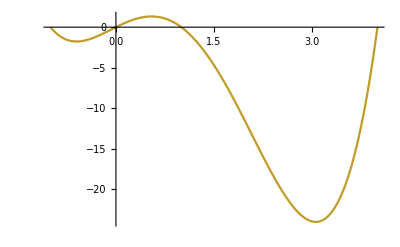

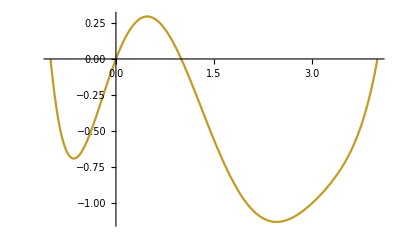

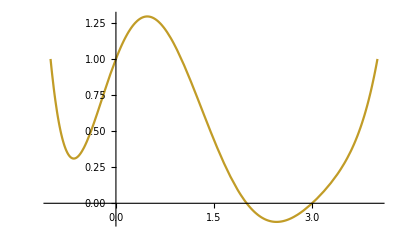

False

False

6-5 x+x^2

```mathematica
sol1//N
s1=a^2((x-b)^2+c^2)/.sol1;
F=1+s1(x+1)x(x-1)(x-4);
Plot[(x+1)x(x-1)(x-4),{x,-1,4}]
Plot[F-1,{x,-1,4}]
Plot[F,{x,-1,4}]
s0=(x-2)(x-3)F;
Reduce[s0<0,x]
Reduce[s1<0,x]
s0+s1 g//Simplify
```